```mathematica
(*Bloque para cargar MaTeX*)
ResourceFunction["MaTeXInstall"][];
ConfigureMaTeX["Ghostscript"->"C:\\Program Files\\gs\\gs10.03.0\\bin\\gswin64c.exe"];
ConfigureMaTeX["pdfLaTeX" -> "C:\\texlive\\2024\\bin\\windows\\pdflatex.exe"]
<<MaTeX`;
MaTeX["x^2"]
```

ConfigureMaTeX[pdfLaTeX→C:\texlive\2024\bin\windows\pdflatex.exe]

ConfigureMaTeX::shdw: Symbol ConfigureMaTeX appears in multiple contexts {MaTeX`,Global`}; definitions in context MaTeX` may shadow or be shadowed by other definitions.

-Graphics-

```mathematica
ν=1/3;
```

Relacion Original simetrica

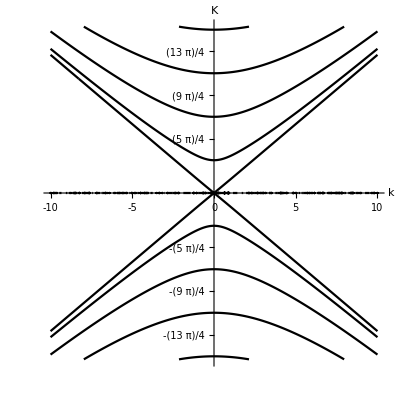

```mathematica
ContourPlot[Sqrt[Kw^2-k^2]*(Kw^2+(1-ν)k^2)^2 *Cosh[Sqrt[Kw^2+k^2]]*Sin[Sqrt[Kw^2-k^2]]+
Sqrt[Kw^2+k^2]*(Kw^2-(1-ν)k^2)^2 *Sinh[Sqrt[Kw^2+k^2]]*Cos[Sqrt[Kw^2-k^2]]==0,{k,-10,10},{Kw,-12,12}, PlotTheme->"Monochrome", Frame->False,Axes->True,AxesLabel->{k,K}, Ticks->{{-10,-5,0,5,10},{-5Pi/4,-9Pi/4, -13Pi/4,5Pi/4,9Pi/4, 13Pi/4}}, MaxRecursion->5]
```

Relacion original antisimetrica

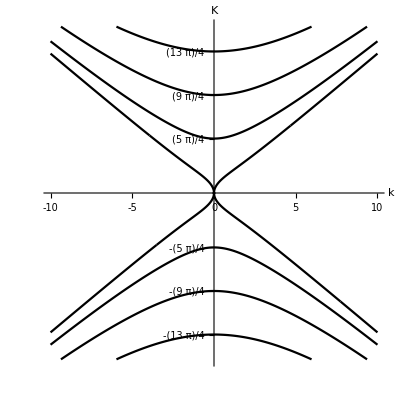

```mathematica
ContourPlot[Sqrt[Kw^2+k^2]*(Kw^2-(1-ν)k^2.)^2 *Sin[Sqrt[Kw^2-k^2]]- 
Sqrt[Kw^2-k^2]*(Kw^2+(1-ν)k^2)^2 *Tanh[Sqrt[Kw^2+k^2]]*Cos[Sqrt[Kw^2-k^2]]==0.,{k,-10,10},{Kw,-12,12}, MaxRecursion->6, PerformanceGoal->"Quality", PlotTheme->"Monochrome", Frame->False,Axes->True,AxesLabel->{k,K}, Ticks->{{-10,-5,0,5,10},{-5Pi/4,-9Pi/4, -13Pi/4,5Pi/4,9Pi/4, 13Pi/4}}]
```

Relacion de dispersion simetrica

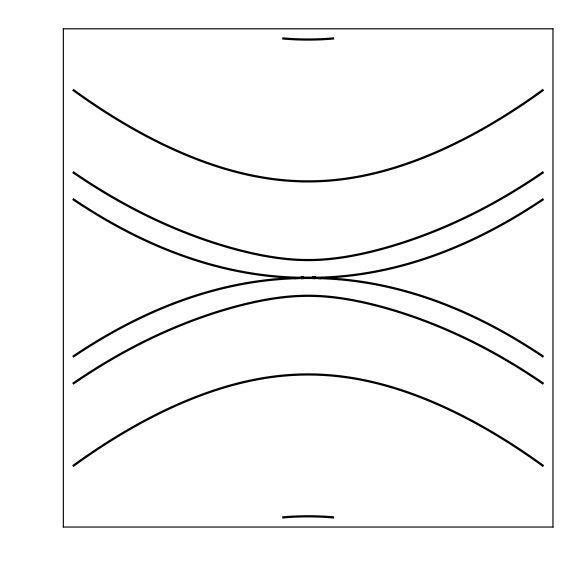

```mathematica
p1 = graficaSimetrica=ContourPlot[Sqrt[Abs[w]-k^2]*(Abs[w]+(1-ν)k^2)^2 *Cosh[Sqrt[Abs[w]+k^2]/2]*Sin[Sqrt[Abs[w]-k^2]/2]+
Sqrt[Abs[w]+k^2]*(Abs[w]-(1-ν)k^2)^2 *Sinh[Sqrt[Abs[w]+k^2]/2]*Cos[Sqrt[Abs[w]-k^2]/2]==0,{k,-10,10},{w,-300,300}, PlotTheme->"Monochrome", MaxRecursion->5, ImageSize->Large, Frame->True,FrameStyle->Directive[{Black,Thick}], GridLines->Automatic,
LabelStyle->{FontFamily->"CMU Serif", FontSize->20}, 
FrameLabel->{
MaTeX["kW", Magnification->2], 
MaTeX["\\omega/\\mathring{\\omega}", Magnification->2]},
FrameTicks->{
{Table[{j,MaTeX[j,Magnification->1.8]},{j,Range[-300,300,100]}] (*y axis*),None},{Table[{j,MaTeX[j,Magnification->1.8]},{j,Range[-20,20,10]}] (*x axis*),None}
}]
```

```mathematica
Export["simetrica.pdf", graficaSimetrica]
```

simetrica.pdf

```mathematica
Export["antisimetrica.pdf", antisimetrica]
```

antisimetrica.pdf

Relación de Dispersión Antisimétrica

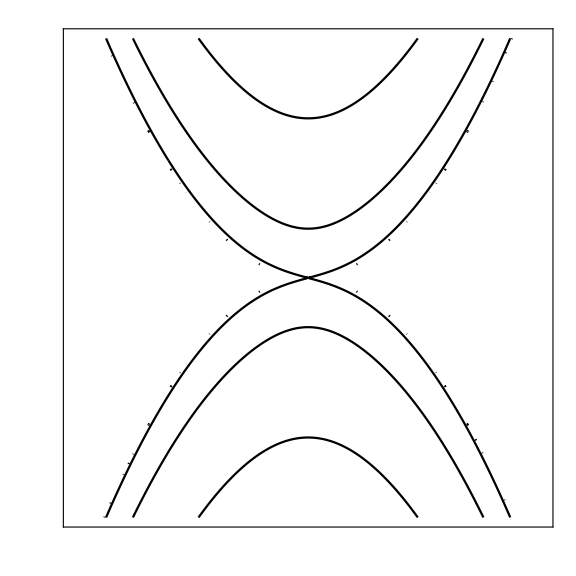

$Aborted

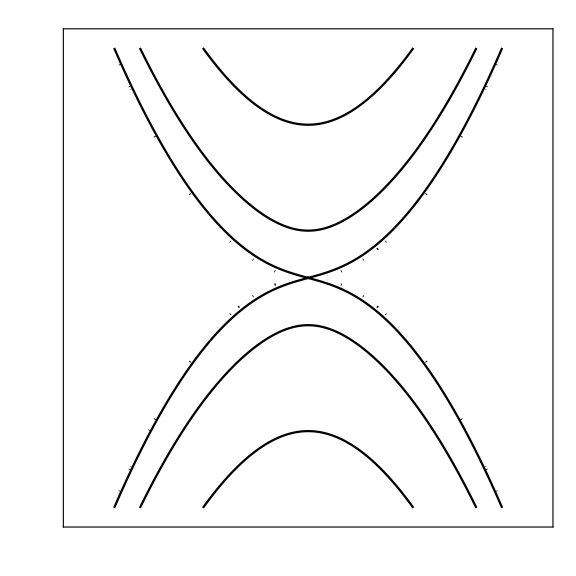

```mathematica
antisimetrica=ContourPlot[Sqrt[Abs[w]+k^2]*(Abs[w]-(1-ν)k^2)^(2) *Cosh[Sqrt[Abs[w]+k^2]/2]*Sin[Sqrt[Abs[w]-k^2]/2]-
Sqrt[Abs[w]-k^2]*(Abs[w]+(1-ν)k^2)^(2) *Sinh[Sqrt[Abs[w]+k^2]/2]*Cos[Sqrt[Abs[w]-k^2]/2]==0,{k,-20,20},{w,-300,300}, PlotTheme->"Monochrome", MaxRecursion->5,  ImageSize->Large, Frame->True,FrameStyle->Directive[{Black,Thick}], GridLines->Automatic,
LabelStyle->{FontFamily->"CMU Serif", FontSize->20}, 
FrameLabel->{
MaTeX["kW", Magnification->2], 
MaTeX["\\omega/\\mathring{\\omega}", Magnification->2]},
FrameTicks->{
{Table[{j,MaTeX[j,Magnification->1.8]},{j,Range[-300,300,100]}] (*y axis*),None},{Table[{j,MaTeX[j,Magnification->1.8]},{j,Range[-20,20,10]}] (*x axis*),None}
}]
```

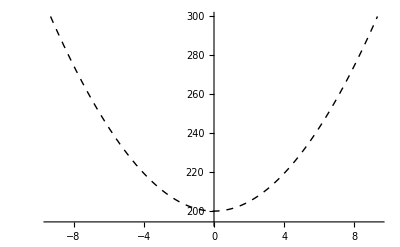

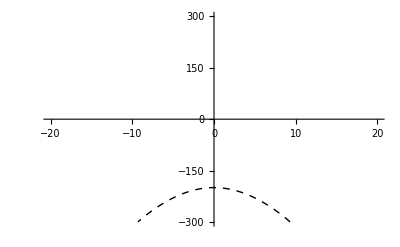

```mathematica
puntosAntiSimetrica = Flatten[Cases[Normal@antisimetrica,Line[x_]:>x,Infinity],1];
puntosAntiSimetrica200=Cases[puntosAntiSimetrica,x_/;Abs[x[[2]]-200-x[[1]]^2]<20 ];
puntosAntiSimetrica60=Cases[puntosAntiSimetrica,x_/;Abs[x[[2]]-60-x[[1]]^2]<20 ];
puntosAntiSimetricam60=Cases[puntosAntiSimetrica,x_/;Abs[-x[[2]]-60-x[[1]]^2]<20 ];
puntosAntiSimetricam200=Cases[puntosAntiSimetrica,x_/;Abs[-x[[2]]-200-x[[1]]^2]<20 ];
plotAntiSim200= ListPlot[puntosAntiSimetrica200, Joined->True, PlotStyle->{Black,Dashed,Thick}]
plotAntiSim60= ListPlot[puntosAntiSimetrica60, Joined->True, PlotStyle->{Black,Dashed,Thick}];
plotAntiSim0=Plot[x^2, {x, -20, 20}, PlotStyle->{Black,Dashed,Thick}];
plotAntiSimm0 = Plot[-x^2, {x, -20, 20}, PlotStyle->{Black,Dashed,Thick}];
plotAntiSimm60= ListPlot[puntosAntiSimetricam60, Joined->True, PlotStyle->{Black,Dashed,Thick}];
plotAntiSimm200= ListPlot[puntosAntiSimetricam200, Joined->True, PlotStyle->{Black,Dashed,Thick}, PlotRange->{{-20,20},{-300,300}}]
```

```mathematica
cutoffFrequency0 =Plot[0, {x, -200,200}, PlotStyle->{Thick, Red, DotDashed}, LabelStyle->{FontFamily->"CMU Serif", FontSize->20}];
cutoffFrequency60 =Plot[61.6728, {x, -200,200}, PlotStyle->{Thick, Red, DotDashed}, LabelStyle->{FontFamily->"CMU Serif", FontSize->20}];
cutoffFrequencym60 =Plot[-61.6728, {x, -200,200}, PlotStyle->{Thick, Red, DotDashed}, LabelStyle->{FontFamily->"CMU Serif", FontSize->20}];
cutoffFrequency200=Plot[{199.859, -199.859}, {x, -200,200}, PlotStyle->{{Thick, Red, DotDashed},{Thick, Red, DotDashed}}];
```

```mathematica
frecuenciaωSimPositivo[0.0, 200]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

199.859

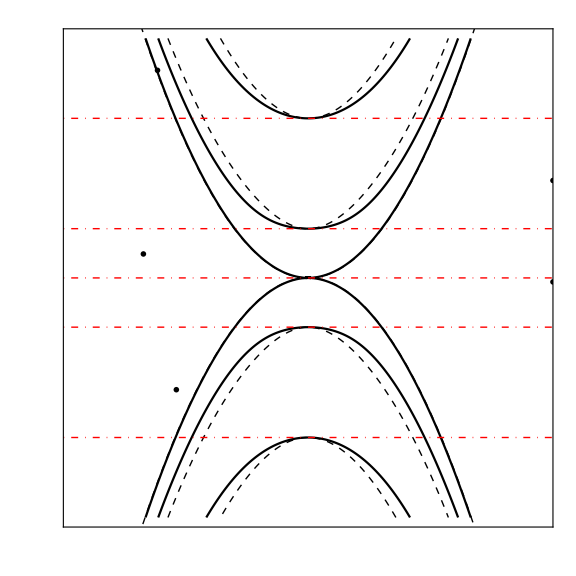

```mathematica
graficaRelacionesDispersionCutOffs = Show[graficaSimetrica, plotAntiSim200, plotAntiSim60, plotAntiSim0, plotAntiSimm0, plotAntiSimm60, plotAntiSimm200,cutoffFrequency0 ,cutoffFrequency60, cutoffFrequencym60, cutoffFrequency200,Epilog->{Inset[MaTeX["KW=0",Magnification->1.7],{-17.5,30},Scaled[{1,1}]], Inset[MaTeX["KW=\\frac{5\\pi}{2}",Magnification->1.7],{26,122},Scaled[{1,1}]],
Inset[MaTeX["KW=\\frac{9\\pi}{2}",Magnification->1.7],{-16,260},Scaled[{1,1}]],Inset[MaTeX["KW=\\frac{-9\\pi}{2}",Magnification->1.7],{-14,-140},Scaled[{1,1}]],Inset[MaTeX["KW=\\frac{-5\\pi}{2}",Magnification->1.7],{26,-5},Scaled[{1,1}]] }, PlotRange->{{-25,25},{-300,300}}]
```

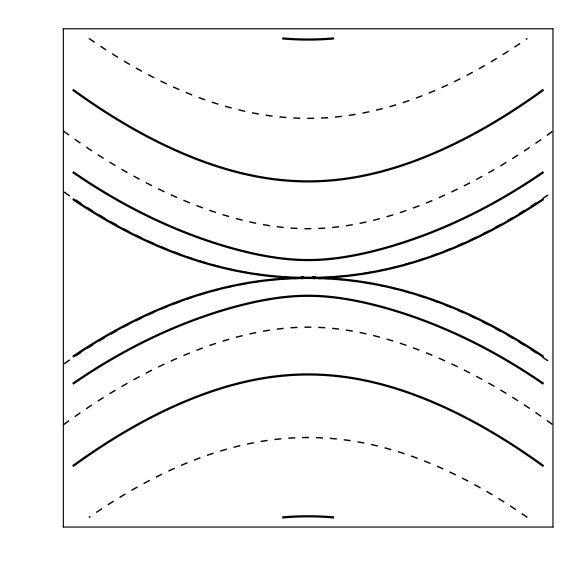

```mathematica
graficaRelacionesDispersion = Show[graficaSimetrica, plotAntiSim200, plotAntiSim60, plotAntiSim0, plotAntiSimm0, plotAntiSimm60,plotAntiSimm200, PlotRange->{{-10,10},{-300,300}}]
```

```mathematica
Export["relacionesDispersionCutOffs.pdf", graficaRelacionesDispersionCutOffs]
```

relacionesDispersionCutOffs.pdf

{}

```mathematica
puntosAntiSimetrica[[4]][[2]]
```

-136.607

Despejando a la frecuencia

```mathematica
frecuenciaωSimPositivo[waveNumber_, offset_]:= Re[w/.First[With[{k=waveNumber}, FindRoot[Sqrt[w-k^2]*(w+(1-ν)k^2)^2 *Cosh[Sqrt[w+k^2]/2]*Sin[Sqrt[w-k^2]/2]-
Sqrt[w+k^2]*(w-(1-ν)k^2)^2 *Sinh[Sqrt[w+k^2]/2]*Cos[Sqrt[w-k^2]/2]==0,{w,Abs[k]^2+offset}, WorkingPrecision->MachinePrecision]]]];
frecuenciaωSimNegativo[waveNumber_, offset_]:= Re[w/.First[With[{k=waveNumber}, FindRoot[Sqrt[w-k^2]*(w+(1-ν)k^2)^2 *Cosh[Sqrt[w+k^2]/2]*Sin[Sqrt[w-k^2]/2]-
Sqrt[w+k^2]*(w-(1-ν)k^2)^2 *Sinh[Sqrt[w+k^2]/2]*Cos[Sqrt[w-k^2]/2]==0,{w,-Abs[k]^2+offset}, WorkingPrecision->MachinePrecision]]]];
frecuenciaωAntiSimPositivo[waveNumber_, offset_]:= Re[w/.First[With[{k=waveNumber}, FindRoot[Sqrt[w+k^2]*(w-(1-ν)k^2)^2 *Tan[Sqrt[w-k^2]/2]-
Sqrt[w-k^2]*(w+(1-ν)k^2)^2 *Tanh[Sqrt[w+k^2]/2]==0,{w,Abs[k]+offset}, WorkingPrecision->20]]]];
frecuenciaωAntiSimNegativo[waveNumber_, offset_]:= Re[w/.First[With[{k=waveNumber}, FindRoot[Sqrt[w+k^2]*(w-(1-ν)k^2)^2 *Cosh[Sqrt[w+k^2]/2]*Sin[Sqrt[w-k^2]/2]-
Sqrt[w-k^2]*(w+(1-ν)k^2)^2 *Sinh[Sqrt[w+k^2]/2]*Cos[Sqrt[w-k^2]/2]==0,{w,-Abs[k]^2+offset}, WorkingPrecision->MachinePrecision]]]];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

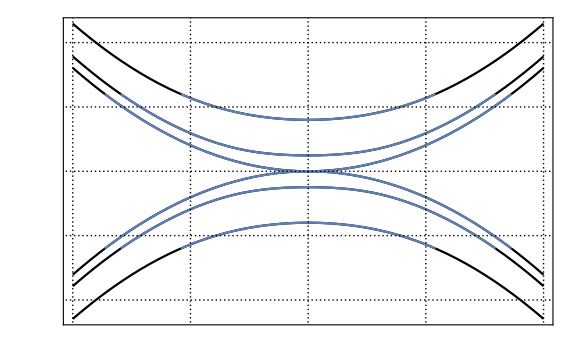

```mathematica
dispersionRelationP1=Plot[frecuenciaωSimPositivo[x,0.0],{x, -20,20},  PlotTheme->"Monochrome", ImageSize->Large, Frame->True,FrameStyle->Directive[{Black,Thick}], GridLines->Automatic,
LabelStyle->{FontFamily->"CMU Serif", FontSize->20}, 
FrameLabel->{
MaTeX["kW", Magnification->2], 
MaTeX["\\omega/\\mathring{\\omega}", Magnification->2]},
FrameTicks->{
{Table[{j,MaTeX[j,Magnification->1.8]},{j,Range[-500,500,250]}] (*y axis*),None},{Table[{j,MaTeX[j,Magnification->1.8]},{j,Range[-20,20,10]}] (*x axis*),None}
}];
dispersionRelationP2=Plot[frecuenciaωSimPositivo[x,60.0],{x, -20,20},  PlotTheme->"Monochrome", ImageSize->Large, Frame->True,FrameStyle->Directive[{Black,Thick}], GridLines->Automatic,
LabelStyle->{FontFamily->"CMU Serif", FontSize->20}, 
FrameLabel->{
MaTeX["kW", Magnification->2], 
MaTeX["\\omega/\\mathring{\\omega}", Magnification->2]},
FrameTicks->{
{Table[{j,MaTeX[j,Magnification->1.8]},{j,Range[-300,300,100]}] (*y axis*),None},{Table[{j,MaTeX[j,Magnification->1.8]},{j,Range[-20,20,20]}] (*x axis*),None}
}];
dispersionRelationP3=Plot[frecuenciaωSimPositivo[x,200.0],{x, -20,20},  PlotTheme->"Monochrome", ImageSize->Large, Frame->True,FrameStyle->Directive[{Black,Thick}], GridLines->Automatic,
LabelStyle->{FontFamily->"CMU Serif", FontSize->20}, 
FrameLabel->{
MaTeX["kW", Magnification->2], 
MaTeX["\\omega/\\mathring{\\omega}", Magnification->2]},
FrameTicks->{
{Table[{j,MaTeX[j,Magnification->1.8]},{j,Range[-300,300,100]}] (*y axis*),None},{Table[{j,MaTeX[j,Magnification->1.8]},{j,Range[-20,20,10]}] (*x axis*),None}
}];
dispersionRelationP4=Plot[frecuenciaωSimNegativo[x,0.0],{x, -20,20},  PlotTheme->"Monochrome", ImageSize->Large, Frame->True,FrameStyle->Directive[{Black,Thick}], GridLines->Automatic,
LabelStyle->{FontFamily->"CMU Serif", FontSize->20}, 
FrameLabel->{
MaTeX["kW", Magnification->2], 
MaTeX["\\omega/\\mathring{\\omega}", Magnification->2]},
FrameTicks->{
{Table[{j,MaTeX[j,Magnification->1.8]},{j,Range[-300,300,100]}] (*y axis*),None},{Table[{j,MaTeX[j,Magnification->1.8]},{j,Range[-20,20,10]}] (*x axis*),None}
}];
dispersionRelationP5=Plot[frecuenciaωSimNegativo[x,-60.0],{x, -20,20},  PlotTheme->"Monochrome", ImageSize->Large, Frame->True,FrameStyle->Directive[{Black,Thick}], GridLines->Automatic,
LabelStyle->{FontFamily->"CMU Serif", FontSize->20}, 
FrameLabel->{
MaTeX["kW", Magnification->2], 
MaTeX["\\omega/\\mathring{\\omega}", Magnification->2]},
FrameTicks->{
{Table[{j,MaTeX[j,Magnification->1.8]},{j,Range[-300,300,100]}] (*y axis*),None},{Table[{j,MaTeX[j,Magnification->1.8]},{j,Range[-20,20,10]}] (*x axis*),None}
}];
dispersionRelationP6=Plot[frecuenciaωSimNegativo[x,-200.0],{x, -20,20},  PlotTheme->"Monochrome", ImageSize->Large, Frame->True,FrameStyle->Directive[{Black,Thick}], GridLines->Automatic,
LabelStyle->{FontFamily->"CMU Serif", FontSize->20}, 
FrameLabel->{
MaTeX["kW", Magnification->2], 
MaTeX["\\omega/\\mathring{\\omega}", Magnification->2]},
FrameTicks->{
{Table[{j,MaTeX[j,Magnification->1.8]},{j,Range[-300,300,100]}] (*y axis*),None},{Table[{j,MaTeX[j,Magnification->1.8]},{j,Range[-20,20,10]}] (*x axis*),None}
}];
SimetricDispersionRelation=Show[dispersionRelationP1, dispersionRelationP2, dispersionRelationP3, dispersionRelationP4, dispersionRelationP5, dispersionRelationP6, p1, PlotRange->All]
```

FindRoot::precw: The precision of the argument function ((-66.6612+w)^2 √(99.9918+w) Tan[(√(-99.9918+w))/2]-√(-99.9918+w) (66.6612+w)^2 Tanh[(√(99.9918+w))/2]==0) is less than WorkingPrecision (20.).

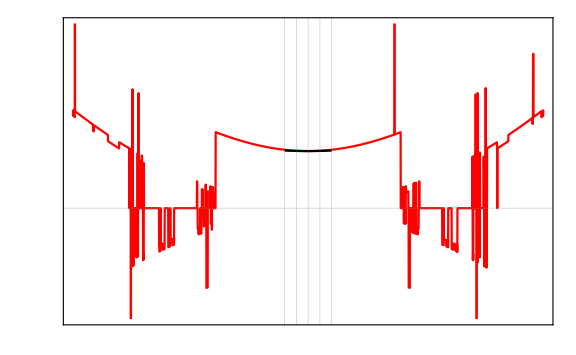

```mathematica
dispersionRelationAntiSP1=Plot[frecuenciaωAntiSimPositivo[x,60.0],{x, -10,10},PlotStyle->Red,ImageSize->Large, Frame->True,FrameStyle->Directive[{Black,Thick}], GridLines->Automatic,
LabelStyle->{FontFamily->"CMU Serif", FontSize->20}, 
FrameLabel->{
MaTeX["kW", Magnification->2], 
MaTeX["\\omega/\\mathring{\\omega}", Magnification->2]},
FrameTicks->{
{Table[{j,MaTeX[j,Magnification->1.8]},{j,Range[-500,500,250]}] (*y axis*),None},{Table[{j,MaTeX[j,Magnification->1.8]},{j,Range[-1,1,0.5]}] (*x axis*),None}
}];
dispersionRelationAntiSP2=Plot[frecuenciaωSimPositivo[x,60.0],{x, -1,1},  PlotTheme->"Monochrome", ImageSize->Large, Frame->True,FrameStyle->Directive[{Black,Thick}], GridLines->Automatic,
LabelStyle->{FontFamily->"CMU Serif", FontSize->20}, 
FrameLabel->{
MaTeX["kW", Magnification->2], 
MaTeX["\\omega/\\mathring{\\omega}", Magnification->2]},
FrameTicks->{
{Table[{j,MaTeX[j,Magnification->1.8]},{j,Range[-300,300,100]}] (*y axis*),None},{Table[{j,MaTeX[j,Magnification->1.8]},{j,Range[-20,20,20]}] (*x axis*),None}
}];(*
dispersionRelationP3=Plot[frecuenciaωSimPositivo[x,200.0],{x, -20,20},  PlotTheme->"Monochrome", ImageSize->Large, Frame->True,FrameStyle->Directive[{Black,Thick}], GridLines->Automatic,
LabelStyle->{FontFamily->"CMU Serif", FontSize->20}, 
FrameLabel->{
MaTeX["kW", Magnification->2], 
MaTeX["\\omega/\\mathring{\\omega}", Magnification->2]},
FrameTicks->{
{Table[{j,MaTeX[j,Magnification->1.8]},{j,Range[-300,300,100]}] (*y axis*),None},{Table[{j,MaTeX[j,Magnification->1.8]},{j,Range[-20,20,10]}] (*x axis*),None}
}];
dispersionRelationP4=Plot[frecuenciaωSimNegativo[x,0.0],{x, -20,20},  PlotTheme->"Monochrome", ImageSize->Large, Frame->True,FrameStyle->Directive[{Black,Thick}], GridLines->Automatic,
LabelStyle->{FontFamily->"CMU Serif", FontSize->20}, 
FrameLabel->{
MaTeX["kW", Magnification->2], 
MaTeX["\\omega/\\mathring{\\omega}", Magnification->2]},
FrameTicks->{
{Table[{j,MaTeX[j,Magnification->1.8]},{j,Range[-300,300,100]}] (*y axis*),None},{Table[{j,MaTeX[j,Magnification->1.8]},{j,Range[-20,20,10]}] (*x axis*),None}
}];
dispersionRelationP5=Plot[frecuenciaωSimNegativo[x,-60.0],{x, -20,20},  PlotTheme->"Monochrome", ImageSize->Large, Frame->True,FrameStyle->Directive[{Black,Thick}], GridLines->Automatic,
LabelStyle->{FontFamily->"CMU Serif", FontSize->20}, 
FrameLabel->{
MaTeX["kW", Magnification->2], 
MaTeX["\\omega/\\mathring{\\omega}", Magnification->2]},
FrameTicks->{
{Table[{j,MaTeX[j,Magnification->1.8]},{j,Range[-300,300,100]}] (*y axis*),None},{Table[{j,MaTeX[j,Magnification->1.8]},{j,Range[-20,20,10]}] (*x axis*),None}
}];
dispersionRelationP6=Plot[frecuenciaωSimNegativo[x,-200.0],{x, -20,20},  PlotTheme->"Monochrome", ImageSize->Large, Frame->True,FrameStyle->Directive[{Black,Thick}], GridLines->Automatic,
LabelStyle->{FontFamily->"CMU Serif", FontSize->20}, 
FrameLabel->{
MaTeX["kW", Magnification->2], 
MaTeX["\\omega/\\mathring{\\omega}", Magnification->2]},
FrameTicks->{
{Table[{j,MaTeX[j,Magnification->1.8]},{j,Range[-300,300,100]}] (*y axis*),None},{Table[{j,MaTeX[j,Magnification->1.8]},{j,Range[-20,20,10]}] (*x axis*),None}
}];*)
Show[dispersionRelationAntiSP1, dispersionRelationAntiSP2, PlotRange->All]
```

```mathematica
data1 = Table[{x,frecuenciaωAntiSimPositivo[x,0.0]}, {x,-1.0, 1.0, 0.01 }];
data2= Table[{x,frecuenciaωAntiSimPositivo[x, 60.0]}, {x,-3.0, 3.0, 0.01}];
data3=Table[{x,frecuenciaωAntiSimPositivo[x, 200.0]}, {x, -5,5, 0.05}];
data4 = Table[{x,frecuenciaωAntiSimNegativo[x,0.0]}, {x,-1.0, 1.0, 0.01 }];
data5= Table[{x,frecuenciaωAntiSimNegativo[x, -60.0]}, {x,-3.0, 3.0, 0.01}];
data6=Table[{x,frecuenciaωAntiSimNegativo[x, -200.0]}, {x, -5,5, 0.05}];
```

FindRoot::precw: The precision of the argument function ((-0.666667+w)^2 √(1.+w) Tan[(√(-1.+w))/2]-√(-1.+w) (0.666667+w)^2 Tanh[(√(1.+w))/2]==0) is less than WorkingPrecision (20.).

FindRoot::precw: The precision of the argument function ((-0.6534+w)^2 √(0.9801+w) Tan[(√(-0.9801+w))/2]-√(-0.9801+w) (0.6534+w)^2 Tanh[(√(0.9801+w))/2]==0) is less than WorkingPrecision (20.).

FindRoot::precw: The precision of the argument function ((-0.640267+w)^2 √(0.9604+w) Tan[(√(-0.9604+w))/2]-√(-0.9604+w) (0.640267+w)^2 Tanh[(√(0.9604+w))/2]==0) is less than WorkingPrecision (20.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function ((-6.+w)^2 √(9.+w) Tan[(√(-9.+w))/2]-√(-9.+w) (6.+w)^2 Tanh[(√(9.+w))/2]==0) is less than WorkingPrecision (20.).

FindRoot::precw: The precision of the argument function ((-5.96007+w)^2 √(8.9401+w) Tan[(√(-8.9401+w))/2]-√(-8.9401+w) (5.96007+w)^2 Tanh[(√(8.9401+w))/2]==0) is less than WorkingPrecision (20.).

FindRoot::precw: The precision of the argument function ((-5.92027+w)^2 √(8.8804+w) Tan[(√(-8.8804+w))/2]-√(-8.8804+w) (5.92027+w)^2 Tanh[(√(8.8804+w))/2]==0) is less than WorkingPrecision (20.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 20. digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function ((-16.6667+w)^2 √(25.+w) Tan[(√(-25.+w))/2]-√(-25.+w) (16.6667+w)^2 Tanh[(√(25.+w))/2]==0) is less than WorkingPrecision (20.).

FindRoot::precw: The precision of the argument function ((-16.335+w)^2 √(24.5025+w) Tan[(√(-24.5025+w))/2]-√(-24.5025+w) (16.335+w)^2 Tanh[(√(24.5025+w))/2]==0) is less than WorkingPrecision (20.).

FindRoot::precw: The precision of the argument function ((-16.0067+w)^2 √(24.01+w) Tan[(√(-24.01+w))/2]-√(-24.01+w) (16.0067+w)^2 Tanh[(√(24.01+w))/2]==0) is less than WorkingPrecision (20.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 20. digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

```mathematica
antiSimetrica1= Fit[data1, {1, x, x^2}, x]
```

-1.4805×10^-16+1. x^2

```mathematica
antiSimetrica2 = Fit[data2, {1, x, x^2}, x]
```

61.7249+1.36546 x^2

```mathematica
antiSimetrica3 = Fit[data3, {1, x, x^2}, x]
```

199.925-3.79237×10^-15 x+1.20877 x^2

```mathematica
antiSimetrica4 = Fit[data4, {1, x, x^2}, x]
```

1.4805×10^-16-1. x^2

```mathematica
antiSimetrica5 = Fit[data5, {1, x, x^2}, x]
```

-61.7249-6.68236×10^-16 x-1.36546 x^2

```mathematica
antiSimetrica6 = Fit[data6, {1, x, x^2}, x]
```

-199.925+5.17438×10^-15 x-1.20877 x^2

```mathematica
fitAntiSP1=Plot[antiSimetrica1,{x, -20,20},PlotStyle->Red,ImageSize->Large, Frame->True,FrameStyle->Directive[{Black,Thick}], GridLines->Automatic,
LabelStyle->{FontFamily->"CMU Serif", FontSize->20}, 
FrameLabel->{
MaTeX["kW", Magnification->2], 
MaTeX["\\omega/\\mathring{\\omega}", Magnification->2]},
FrameTicks->{
{Table[{j,MaTeX[j,Magnification->1.8]},{j,Range[-500,500,250]}] (*y axis*),None},{Table[{j,MaTeX[j,Magnification->1.8]},{j,Range[-20,20,10]}] (*x axis*),None}
}];
fitAntiSP2=Plot[antiSimetrica2,{x, -20,20},PlotStyle->Red,ImageSize->Large, Frame->True,FrameStyle->Directive[{Black,Thick}], GridLines->Automatic,
LabelStyle->{FontFamily->"CMU Serif", FontSize->20}, 
FrameLabel->{
MaTeX["kW", Magnification->2], 
MaTeX["\\omega/\\mathring{\\omega}", Magnification->2]},
FrameTicks->{
{Table[{j,MaTeX[j,Magnification->1.8]},{j,Range[-500,500,250]}] (*y axis*),None},{Table[{j,MaTeX[j,Magnification->1.8]},{j,Range[-20,20,10]}] (*x axis*),None}
}];
```

```mathematica
fitAntiSP3=Plot[antiSimetrica3,{x, -20,20},PlotStyle->Red,ImageSize->Large, Frame->True,FrameStyle->Directive[{Black,Thick}], GridLines->Automatic,
LabelStyle->{FontFamily->"CMU Serif", FontSize->20}, 
FrameLabel->{
MaTeX["kW", Magnification->2], 
MaTeX["\\omega/\\mathring{\\omega}", Magnification->2]},
FrameTicks->{
{Table[{j,MaTeX[j,Magnification->1.8]},{j,Range[-500,500,250]}] (*y axis*),None},{Table[{j,MaTeX[j,Magnification->1.8]},{j,Range[-20,20,10]}] (*x axis*),None}
}];
fitAntiSN1=Plot[antiSimetrica4,{x, -20,20},PlotStyle->Red,ImageSize->Large, Frame->True,FrameStyle->Directive[{Black,Thick}], GridLines->Automatic,
LabelStyle->{FontFamily->"CMU Serif", FontSize->20}, 
FrameLabel->{
MaTeX["kW", Magnification->2], 
MaTeX["\\omega/\\mathring{\\omega}", Magnification->2]},
FrameTicks->{
{Table[{j,MaTeX[j,Magnification->1.8]},{j,Range[-500,500,250]}] (*y axis*),None},{Table[{j,MaTeX[j,Magnification->1.8]},{j,Range[-20,20,10]}] (*x axis*),None}
}];
fitAntiSN2=Plot[antiSimetrica5,{x, -20,20},PlotStyle->Red,ImageSize->Large, Frame->True,FrameStyle->Directive[{Black,Thick}], GridLines->Automatic,
LabelStyle->{FontFamily->"CMU Serif", FontSize->20}, 
FrameLabel->{
MaTeX["kW", Magnification->2], 
MaTeX["\\omega/\\mathring{\\omega}", Magnification->2]},
FrameTicks->{
{Table[{j,MaTeX[j,Magnification->1.8]},{j,Range[-500,500,250]}] (*y axis*),None},{Table[{j,MaTeX[j,Magnification->1.8]},{j,Range[-20,20,10]}] (*x axis*),None}
}];
```

```mathematica
fitAntiSN3=Plot[antiSimetrica6,{x, -20,20},PlotStyle->Directive[Red, Thick],ImageSize->Large, Frame->True,FrameStyle->Directive[{Black,Thick}], GridLines->Automatic,
LabelStyle->{FontFamily->"CMU Serif", FontSize->20}, 
FrameLabel->{
MaTeX["kW", Magnification->2], 
MaTeX["\\omega/\\mathring{\\omega}", Magnification->2]},
FrameTicks->{
{Table[{j,MaTeX[j,Magnification->1.8]},{j,Range[-500,500,250]}] (*y axis*),None},{Table[{j,MaTeX[j,Magnification->1.8]},{j,Range[-20,20,10]}] (*x axis*),None}
}];
```

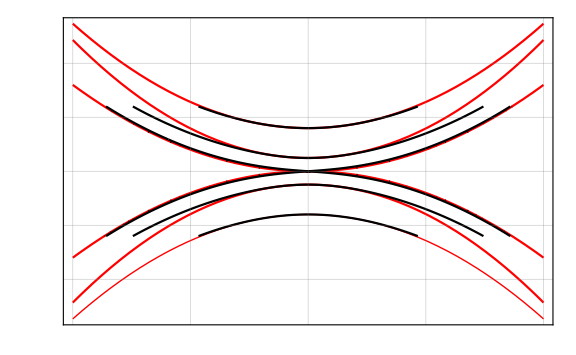

```mathematica
Show[fitAntiSP1, fitAntiSP2, fitAntiSP3, fitAntiSN1, fitAntiSN2, fitAntiSN3, antisimetrica, PlotRange->All]
```

```mathematica
Style[MaTeX["K"], 30]
```

-Graphics-

```mathematica
Style["K", 10]
```

K